```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
aRange={{-10,25},Full};
g[x_]:=PDF[NormalDistribution[5,5],x]
gActual=Rotate[Plot[g[x],{x,-10,25},Frame->{True,True,False,False},FrameTicks->{False,False,False,False},FrameLabel->{"θ",Rotate["p(θ|data)",Pi]},PlotStyle->Orange,PlotRange->aRange,Axes->None],Pi/2];
fProposal[θ_,σ_]:=RandomVariate[NormalDistribution[θ,σ],{1}][[1]]
fSingleStepMetropolis[θ_,σ_,aF_]:=Module[{aProposedTheta=fProposal[θ,σ],aRand=RandomReal[]},If[aF[aProposedTheta]>aF[θ],aProposedTheta,If[aRand<aF[aProposedTheta]/aF[θ],aProposedTheta,θ]]]
fStepMetropolis[nSteps_,aStart_,σ_,aF_]:=NestList[fSingleStepMetropolis[#,σ,aF]&,aStart,nSteps]
```

```mathematica
fStepMetropolisAdaptive[nSteps_Integer,aStart_,aInitialSigma_,aF_,aCheckLength_Integer,aRunningTotal_Integer,lRunningSample__,aTargetAcceptance_,aSigmaDelta_,lRunningSigma_,aDecrementRate_]:=Module[{lSample=fStepMetropolis[aCheckLength,aStart,aInitialSigma,aF],aNewTotal,aNewSigma,aMeanAcceptance,lNewSigma},aNewTotal=aRunningTotal+Length@lSample; aMeanAcceptance=Mean[If[Abs@#>0,1,0]&/@Differences[lSample]];aNewSigma=If[aMeanAcceptance <aTargetAcceptance ,aInitialSigma - aSigmaDelta,aInitialSigma+aSigmaDelta];lNewSigma=Join[lRunningSigma,{aNewSigma}]; lSample=Join[lRunningSample,lSample]; If[aNewTotal<nSteps,fStepMetropolisAdaptive[nSteps,Last@lSample,aNewSigma,aF,aCheckLength,aNewTotal,lSample,aTargetAcceptance,aDecrementRate aSigmaDelta,lNewSigma,aDecrementRate],{lSample,lNewSigma}]]
```

```mathematica
lTooBig=fStepMetropolisAdaptive[20000,1,50,g,100,0,{},0.44,1,{},1];
```

```mathematica
lTooSmall=fStepMetropolisAdaptive[20000,1,0.1,g,100,0,{},0.44,1,{},1];
```

```mathematica
lAcceptanceBig=If[Abs@#>0,1,0]&/@Differences[lTooBig[[1]]];
lMABig=MovingAverage[lAcceptanceBig,100];
lAcceptanceSmall=If[Abs@#>0,1,0]&/@Differences[lTooSmall[[1]]];
lMASmall=MovingAverage[lAcceptanceSmall,100];
```

```mathematica
xTicks={{0,0},{100,10000},{200,20000},{300,30000},{400,40000}};
aRange={Automatic,{0,55}};
```

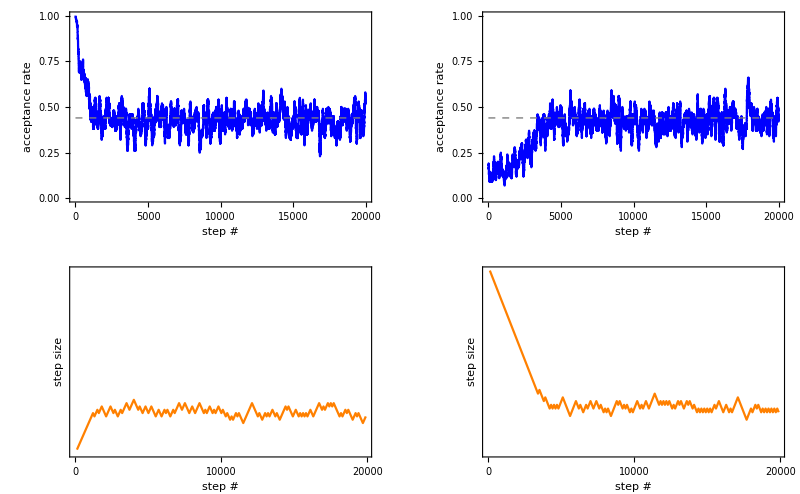

```mathematica
g1=ListLinePlot[lMABig,PlotRange->{Automatic,{0,1}},Frame->{True,True,False,False},BaseStyle->{FontSize->12},FrameLabel->{"step #","acceptance rate"},PlotStyle->Blue,Epilog->{Thick,Dashed,Gray,Line[{{0,0.44},{20000,0.44}}]}];
g2=ListLinePlot[lTooBig[[2]],PlotRange->Full,PlotRange->{Automatic,{0,1}},Frame->{True,True,False,False},BaseStyle->{FontSize->12},FrameLabel->{"step #","step size"},PlotStyle->Orange,FrameTicks->{xTicks,None},PlotRange->aRange];
g1a=ListLinePlot[lMASmall,PlotRange->{Automatic,{0,1}},Frame->{True,True,False,False},BaseStyle->{FontSize->12},FrameLabel->{"step #","acceptance rate"},PlotStyle->Blue,Epilog->{Thick,Dashed,Gray,Line[{{0,0.44},{20000,0.44}}]}];
g2a=ListLinePlot[lTooSmall[[2]],PlotRange->aRange,Frame->{True,True,False,False},BaseStyle->{FontSize->12},FrameLabel->{"step #","step size"},PlotStyle->Orange,FrameTicks->{xTicks,None}];
gFinal=Show[GraphicsGrid[{{g1a,g1},{g2a,g2}}],ImageSize->800]
```

```mathematica
Export["metropolisHastings_acceptanceRate.pdf",gFinal]
```

metropolisHastings_acceptanceRate.pdf